# Test Data Trace Plotting

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Mon 17 Feb 2014 14:50:45)

<<Set JLink` java stack size to 3072Mb>>

«JavaObject[nounou.DataReader]»

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

## Load Data

```mathematica
testDataFileDirectory = "V:\\docs\\k.VSDdata\\project.SPP\\Nlx\\SPP010\\2013-12-02_17-07-31";
```

```mathematica
(* FileNames[testDataFileDirectory<>"\\*"] *)
```

```mathematica
testFiles4=FileNames[testDataFileDirectory<>"\\Tet4*.ncs"]
```

{V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4a.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4b.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4c.ncs,V:\docs\k.VSDdata\project.SPP\Nlx\SPP010\2013-12-02_17-07-31\Tet4d.ncs}

```mathematica
(*Methods[NN]*)
```

```mathematica
$NNReader = NN`newReader[]
```

«JavaObject[nounou.DataReader]»

```mathematica
$NNReader@load[testFiles4]
```

## NNTracePlot

```mathematica
$NNReader@dataFrameSegmentToMs[0,0]
```

0.

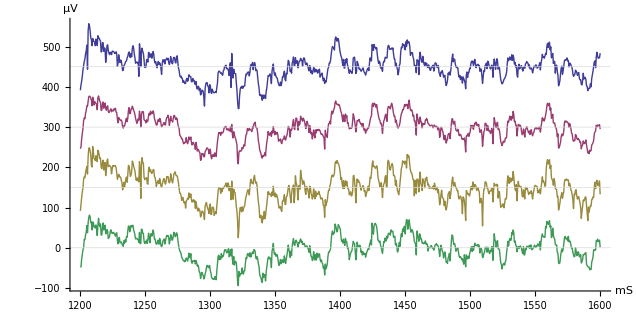

```mathematica
NNTracePlot[ Range[0,3], 1200 ;; 1600 , 0, NNStackLists->150]
```

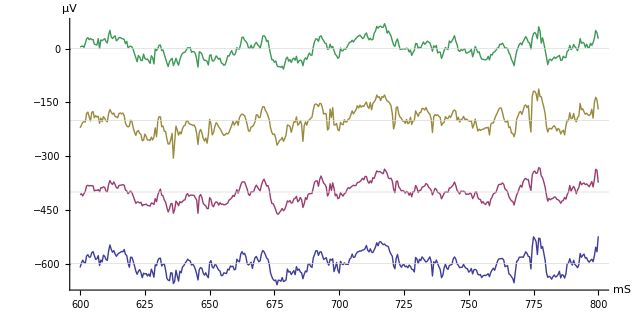

```mathematica
NNTracePlot[ Range[0,3], 600 ;; 800 , 0]
```